```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Read in mat file

```mathematica
Import["Alex_Face_Ref.txt","Elements"]
```

{Data,Lines,Plaintext,String,Summary,Words}

The original meshes

```mathematica
Face=Import["Alex_Face_Ref.txt","Data"]+1;
```

```mathematica
VerticeRef=Import["Alex_Node_Ref.txt","Data"];
```

```mathematica
Dimensions[Face]
```

{7963,3}

```mathematica
Dimensions[VerticeRef]
```

{4096,3}

The parameterization results

```mathematica
UV=Import["Alex_UV.txt","Data"];
```

The principal directions and curvatures of the reference surface

```mathematica
PD1Ref=Import["Alex_PD1_Ref.txt","Data"];
PD2Ref=Import["Alex_PD2_Ref.txt","Data"];
k1Ref=Flatten[Import["Alex_k1_Ref.txt","Data"]];
k2Ref=Flatten[Import["Alex_k2_Ref.txt","Data"]];
```

```mathematica
Dimensions[k1Ref]
```

{4096}

```mathematica
nNodes=Dimensions[VerticeRef][[1]]
nFaces=Dimensions[Face][[1]]
```

4096

7963

```mathematica
Table[{{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,1]],3]]},{VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,2]],3]]},{VerticeRef[[Face[[n,3]],1]],VerticeRef[[Face[[n,3]],2]],VerticeRef[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelRef=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Table[{{UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],0},{UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],0},{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],0}},{n,1,nFaces}];
UVPlane=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Show[ModelRef,UVPlane]
```

-Graphics3D-

检查一下由Libigl计算的UV平面圆有多大

```mathematica
Max[UV[[All,1]]]-Min[UV[[All,1]]]
```

2

```mathematica
Max[UV[[All,2]]]-Min[UV[[All,2]]]
```

1.99993

是一个半径几乎为1的圆

接下来要在半径几乎为1的圆上生成规则的网格，标准化的网格

方法2：采用Mathematica提供的函数实现离散化

```mathematica
Rad=1;
FactorAssemb=0.001;
MeshSize=0.0005;
```

```mathematica
unitDisk=Disk[{0,0},Rad-FactorAssemb];
triangulationDisk=DiscretizeRegion[unitDisk,Method->Continuation,PerformanceGoal->"Quality",MeshQualityGoal->"Maximal",MaxCellMeasure->MeshSize];
Show[triangulationDisk,AspectRatio->Automatic];
```

```mathematica
(*获取节点和单元信息*)
UVRemesh=MeshCoordinates[triangulationDisk];
FaceRemesh=MeshCells[triangulationDisk,2];
(*2 表示获取三角形单元信息*)
```

```mathematica
nNodesRemesh=Dimensions[UVRemesh][[1]]
nFacesRemesh=Dimensions[FaceRemesh][[1]]
FaceRemesh=Table[FaceRemesh[[n,1]],{n,1,nFacesRemesh}];
```

4908

9606

```mathematica
Table[{{UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],0},{UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],0},{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],0}},{n,1,nFacesRemesh}];
Graphics3D[{Directive[RGBColor[0.618,0.618,1],Opacity[0.5]],Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,3]],1]],1/3(VerticeRef[[Face[[n,1]],1]]+VerticeRef[[Face[[n,2]],1]]+VerticeRef[[Face[[n,3]],1]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.0489814,0.516082,0.0252784},{1.,0.076588,0.528417,0.0404704},{1.,0.0517517,0.545398,0.0282253},{1.,0.059107,0.529966,0.0313247}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K21, K22, K23}

```mathematica
MatK2Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,3]],2]],1/3(VerticeRef[[Face[[n,1]],2]]+VerticeRef[[Face[[n,2]],2]]+VerticeRef[[Face[[n,3]],2]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.0489814,0.516082,0.0252784},{1.,0.076588,0.528417,0.0404704},{1.,0.0517517,0.545398,0.0282253},{1.,0.059107,0.529966,0.0313247}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K31, K32, K33}

```mathematica
MatK3Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],3]],VerticeRef[[Face[[n,2]],3]],VerticeRef[[Face[[n,3]],3]],1/3(VerticeRef[[Face[[n,1]],3]]+VerticeRef[[Face[[n,2]],3]]+VerticeRef[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.0489814,0.516082,0.0252784},{1.,0.076588,0.528417,0.0404704},{1.,0.0517517,0.545398,0.0282253},{1.,0.059107,0.529966,0.0313247}} 构成的 Inverse 的结果可能包含明显的数值错误.

Check...

```mathematica
(*ListPlot[Table[MatK1Ref[[n,1]]+MatK1Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Ref[[n,1]]+MatK2Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Ref[[n,1]]+MatK3Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

```mathematica
Dimensions[MatK3Ref]
```

{7963,4}

上面得到了每个单元的K矩阵，可用于查询单元内部各点映射到曲面的坐标。接下来要给新的UV平面节点，匹配它所属的单元。

```mathematica
(*判断点是否位于任意一个三角形中*)
(*inTriangleQ[pt_,triVertices_]:=RegionMember[Triangle[triVertices],pt];*)
inTriangleQ[pt_,triVertices_]:=RegionMember[Polygon[triVertices],pt];
(*定义一个点的坐标*)
point={0.2,0.2};
(*找到包含给定点的三角形*)
triangleIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&]
Position[Face,triangleIndex][[1,1]]
```

{2811,825,2828}

2869

这条路行得通，接下来进入循环，如果新的UV平面圆与初始的平面圆一样大，会导致新的节点有可能落在初始平面圆的外面。于是缩小了一下新的UV平面圆。系数为FactorAssemb

一段计算不完，要分段以避免内存溢出

```mathematica
nNodesRemesh
```

4908

```mathematica
Pos=Table[0,{i,1,nNodesRemesh}];
```

```mathematica
n=1;
While[n<=nNodesRemesh,point={UVRemesh[[n,1]],UVRemesh[[n,2]]};triIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&];Pos[[n]]=Position[Face,triIndex][[1,1]];n++]
```

```mathematica
Pos
```

{7601,7315,2303,7952,5383,5384,5190,3815,7741,7217,2313,7789,2349,2350,7716,7914,5366,7691,16,5368,2413,7900,7870,3810,5370,5365,3811,7438,7314,5372,7652,2293,2590,3814,5360,2294,5357,2618,5358,2295,7956,4724,7934,526,563,591,634,7770,5949,2972,5355,7437,881,3053,969,1030,4602,1129,1231,3231,4899,1416,1475,1532,7877,1608,7297,7686,5350,2301,1750,1789,5345,5344,1876,7471,7632,7609,7308,6183,5341,7490,7906,7688,3664,7586,7613,7922,7203,4379,2222,7208,3768,3774,5335,3785,7933,5336,5337,7636,7636,7293,7423,5331,7422,5328,2278,3801,2277,5326,3806,2284,6993,3808,7599,5324,3807,2283,2282,7510,7420,7754,2276,7850,3799,3792,5441,3790,5446,3759,7205,7723,5397,5448,7335,7954,7634,5442,7213,2290,3557,1972,1937,3506,7274,4284,3461,7468,7239,7180,3392,7864,5425,1488,5159,7581,7581,5422,5421,4085,7798,3129,7819,5419,851,834,767,2874,2299,2300,2300,552,7267,5439,393,7397,307,2601,206,7706,7161,7160,2492,7458,7158,5412,3833,7593,5398,5396,5394,2335,5391,2323,2324,7685,2326,2318,2319,7321,5387,7773,2306,5385,4388,2304,2,2302,5333,7424,6038,2991,7889,7513,5950,7536,1926,3703,3747,7780,3788,7604,3546,1677,1556,7894,3951,7476,2506,2662,615,1402,766,2308,6850,5196,2356,7474,7868,2004,7960,7186,1853,7347,3730,4667,2237,7276,7257,4672,7835,7699,7826,7209,5065,5330,7303,7840,6369,2173,2052,7183,1600,1268,7444,6010,7739,7641,494,7366,4072,7538,6782,2389,2437,2471,392,2697,306,7360,7648,1451,5159,7178,7562,7562,747,7316,5378,6817,6518,6566,2430,5279,2353,7700,7615,7712,7871,7193,3590,7881,7948,5158,7638,7479,7254,3714,7526,7923,3670,3784,7635,7541,7674,7301,7278,7503,3800,7294,7563,7797,7737,7293,2291,7333,4660,7646,5450,3750,2105,7484,7357,7863,7580,7448,7805,5435,7327,7727,7325,7454,5831,442,7452,3106,3145,4607,5371,7596,173,8,2392,3819,2420,7886,7956,7382,7927,525,7651,7282,7762,5425,7859,5949,2307,5380,7952,7416,2335,6734,7218,4678,5803,6647,6308,7493,2352,7318,7735,7746,7389,7533,7559,7872,7307,3631,1599,3316,7640,7311,7929,3479,7428,7491,3481,3725,2244,7728,7404,7933,5334,7364,7616,3764,3798,5332,5278,5067,4675,7261,7262,7554,7210,7598,7473,7842,7856,7450,4660,3528,6370,1877,7647,7204,2162,7659,7942,7250,7181,7271,7891,7582,4085,7876,5420,7326,7453,7853,7331,5418,7588,7166,341,3017,7365,3116,7911,7908,7356,7396,7675,7511,7372,2579,2349,7785,7930,7223,6645,7676,5374,5369,7882,7383,7935,7924,430,7504,590,5356,4428,7794,5913,2309,7315,5380,7672,2305,5407,5391,2325,7323,4393,7221,7460,7226,6461,6310,7579,5388,7938,6303,1951,3321,7697,5348,5171,5351,7436,1324,7506,5343,2210,7568,7200,7407,2250,2277,7259,7375,5947,7844,7626,7421,7196,5937,7026,7199,7391,2260,3419,7861,7185,4291,7915,3129,7822,7457,7497,4774,7583,7338,4060,1129,7958,7499,7785,7716,7731,2350,5367,7492,6454,7340,7902,4431,7418,7939,7790,7846,6,7678,7753,5394,5404,7480,7279,7608,7531,7322,7496,2327,7917,6305,1519,1415,1749,5342,5346,7305,7251,7932,5338,6064,7721,3795,3805,7374,7605,7963,7724,7078,7336,2122,7206,7392,7816,4955,1836,7411,1312,7893,5419,834,5438,4028,5865,1256,7212,7763,7766,7886,7901,7233,7383,7281,7663,6375,3393,2316,5191,7752,5413,7379,7265,5414,5399,7463,207,7466,2353,2393,7705,6433,1417,4917,1348,7916,2040,5339,7695,2106,7334,2258,2240,2241,3769,7854,7953,7270,850,2313,7784,7769,7313,235,2588,1588,2309,2438,5410,7703,7693,7622,2648,6861,2363,2355,4899,3270,3305,2051,7682,2236,2106,2068,6292,2259,7642,7661,7812,7959,4270,4984,4984,3446,1794,7892,1395,872,4005,7500,5951,7806,6355,5912,6273,2316,2330,2438,2429,2403,7231,6607,7630,2633,2351,7918,25,22,7029,24,28,2354,6268,3631,7603,6063,7246,2109,6062,3773,7595,2193,7812,2223,4239,7238,1403,815,4780,5954,6375,2594,268,2599,6437,235,1578,6048,6273,4,3817,6746,6311,6312,2496,6307,18,2354,1486,7955,1425,3580,3758,6416,7645,7472,7950,6282,1476,3279,720,7745,7788,5070,2347,296,3322,1631,5916,2342,7560,6797,5963,236,2465,2366,5198,3828,6405,4911,5607,3763,2251,7642,2127,1796,3333,746,734,2333,4400,6217,4932,6504,5248,1427,1489,1349,3379,7184,2337,6607,6219,35,2356,2374,6306,13,7015,2339,7075,2365,5899,2036,6299,7388,2377,243,3387,2314,6862,7148,1361,6073,2346,6860,1465,1292,2187,2212,4398,2345,6309,6613,6110,4143,1466,5245,4670,2179,5943,6072,5942,5052,2188,2368,5281,4398,4395,270,285,4703,6851,6221,2650,6356,1291,4613,3827,6778,1310,5243,3826,2332,4873,4113,3825,2387,3203,3261,4872,3191,1214,1112,1194,1113,1195,2345,6601,6670,23,6721,21,3824,6546,3820,7339,7243,7607,3748,3734,3742,3735,6120,5187,6120,7742,1870,493,2564,7899,2691,7621,3923,7001,7296,7776,657,7367,2362,7715,7719,7570,7658,7869,1963,1936,7713,1875,7190,7245,7535,7611,2273,3791,2273,7833,2266,5056,7328,7725,7779,553,5835,7523,706,2382,2418,2412,7412,7540,6886,2533,7539,2504,2491,2505,2537,7781,3794,2257,3789,7895,7177,7946,7399,4835,993,4852,4845,5875,5191,5191,5069,3818,4390,2124,2087,2125,2162,1854,1865,7159,2523,7961,2508,5955,2362,2034,3589,5936,2027,2252,7209,7815,4259,2569,6941,4401,6558,433,431,395,3823,3656,3655,3676,2172,3655,6665,6182,7943,5061,2223,6436,5288,6406,3876,5206,4430,5817,6310,2642,315,7880,7960,7505,7524,7684,1531,6270,6506,1484,4147,7207,2184,2186,2174,2174,3665,2139,7295,2370,2381,2370,2371,2369,5073,5954,6122,5281,7164,6209,6680,2591,4427,2596,271,1552,1349,3225,1602,2475,4,2343,43,4975,6927,6335,6404,6335,4880,2312,4392,4676,4676,4114,6075,1180,3820,3486,3460,7478,7242,3709,7909,2463,7897,7910,6995,7435,7417,1661,4959,7179,1695,1614,3344,1695,7949,7571,7694,7478,4246,7830,4774,2410,2401,2441,2408,2416,2417,5957,2390,2417,2407,2419,2428,2428,2426,5066,2272,5188,2274,2267,7298,6644,4840,7289,5430,7237,7947,986,5883,3114,4088,1155,6908,3816,4390,4391,1835,1829,6283,2383,5797,34,2047,5930,2016,7354,5036,2246,4378,6124,4700,200,6695,5197,432,2685,3253,1270,1073,1590,1609,5952,5800,43,5078,4226,6368,1731,1752,4247,1737,1708,1741,1662,7128,5198,6180,3835,17,6077,6123,3835,6448,5284,7401,3723,2470,7076,4231,1718,3437,1615,3343,1518,3337,2424,2436,2435,5956,4685,2380,2400,7299,4383,7508,6443,7175,7594,6486,6557,2310,1794,4294,5926,2384,6206,74,2393,3616,2003,3570,2026,4347,5034,1982,4343,4341,2017,6294,4350,3770,2594,166,4426,4402,6385,3831,4681,6076,6141,7054,2431,495,1376,4884,1157,4854,5889,6097,4095,4083,1141,6031,4884,1072,4082,4082,3168,4079,6990,4061,4080,6106,909,6105,950,4836,1609,1621,4227,1678,4229,2331,10,4396,5193,3822,2405,2440,3836,2511,2497,4407,4407,2203,5213,4636,4948,4630,7072,3363,4959,5263,1715,6540,1516,6709,1485,6766,7070,6766,3342,3296,6873,1561,5911,1585,1393,6897,1613,3247,4947,4682,6373,5074,4404,5957,2424,2425,2455,3832,77,3832,4399,50,41,3832,6808,6739,4685,6565,6142,2452,48,49,78,6604,6884,7299,2234,2253,2250,3778,2248,2249,3054,4294,3522,5797,33,5797,6192,5618,1935,1862,1899,3571,2037,2053,3780,3769,4382,3781,2190,4381,3777,2213,6976,3761,3755,2232,2265,7053,7052,4700,2552,2542,2532,2541,7054,2448,494,4439,598,606,2840,3962,643,6981,724,658,6950,2951,667,5224,736,4152,1334,4918,4033,4235,5796,3821,2415,4680,20,3829,2386,68,29,2376,2396,5960,5961,5960,6207,2514,2415,4687,108,5086,130,3847,2514,159,197,163,99,2593,138,5788,131,87,7015,1680,7025,6046,4631,4197,1561,4209,1289,4879,2454,61,6585,142,6458,89,103,3830,2274,6667,1919,6423,1986,1933,1863,6119,2053,3771,3760,3732,3791,2556,3844,2520,2439,2449,4741,4737,3913,553,4900,3011,3055,19,6937,12,37,6205,2467,2512,2572,2571,3237,3218,1139,6721,101,2255,2242,5945,5063,2271,5062,2216,5062,6882,5696,6926,3739,6881,2225,5650,3739,2206,6924,6879,3762,2207,3727,6302,7066,6350,2219,7681,3746,1878,3531,6423,6201,5619,1971,5014,5014,1950,1970,1874,3476,4281,1828,5651,1846,1842,3502,2069,4359,2123,2080,7065,5058,5087,6885,2532,5082,5806,2562,4689,2489,2477,2477,2471,2502,4414,80,2493,2482,2481,4686,2692,6836,931,901,901,4047,4021,4043,6092,5145,6330,6330,3121,817,2375,44,5794,86,5800,5077,6181,129,5788,2573,4697,2578,2545,6178,7099,6991,1267,7108,4177,5156,1496,5241,69,6924,2196,6301,2215,5650,3649,2165,2225,5182,5280,1861,1845,4289,4290,4269,1809,3451,3475,3708,4374,5058,6372,5944,2214,2199,5060,4695,2518,4419,2530,2529,2516,5085,5201,529,2801,5832,6892,3964,658,3972,4544,5224,5309,832,835,3991,7733,3977,7502,6008,3992,4787,38,5789,57,47,47,60,56,31,5799,30,45,2451,2450,4690,162,95,107,4412,2498,2513,6743,127,189,148,137,6744,2528,3874,4878,4883,4879,3218,6393,6740,1991,7808,1992,7110,7449,7940,1939,6850,6521,5195,6699,5417,7323,6121,5577,1852,5266,5004,4292,4254,3453,3452,3707,3736,2215,2548,2540,4692,4692,4423,5080,2515,2539,6125,467,819,2973,3056,6002,2974,799,6867,2951,817,6422,5078,2485,2414,6846,6846,4688,2603,1229,1290,6100,7941,3530,7157,2361,1889,3435,3475,6986,3745,3744,3731,3844,217,5201,529,6080,371,6594,853,798,3997,708,760,2603,1111,3141,1140,4031,1005,1048,6904,1038,6025,6659,3042,977,1055,3126,3076,4058,4042,4823,4258,3854,4812,4593,4036,4593,4596,6657,979,4596,2831,4828,4825,790,4026,3478,3488,4647,3851,5809,5287,4824,6006,5990,3944,725,684,5103,2786,3997,4810,6619,823,2983,6483,3039,6087,841,4557,6893,705,4011,752,6870,840,6907,6904,870,863,3495,5179,5009,6285,5529,1873,3513,5016,5674,3499,1898,4268,3512,5928,3521,5662,6677,3474,6418,4278,4987,1851,1860,1792,1868,1860,1914,4652,5013,5268,3541,7083,3543,6418,4276,3554,5020,3555,1947,5656,5020,1913,3505,6940,4656,1924,5035,3544,2015,3563,3561,2031,5025,1955,1967,5654,5025,5553,5652,5654,2565,222,186,171,4693,193,187,3867,188,409,170,223,324,3852,2550,205,262,263,3846,2549,224,5808,6468,607,2751,2788,6751,745,7039,3980,6603,5135,6357,6549,7038,6054,1834,4996,4643,3527,5652,225,6216,264,5207,6522,219,6567,292,258,260,6471,279,6425,248,278,2640,2627,7090,599,644,7151,6835,665,682,5673,6395,1815,1772,3868,325,368,325,476,220,2841,2815,6473,4753,7154,6997,3477,6340,4253,3450,1786,5921,4253,4648,1787,5922,6053,1834,1740,3366,4986,1694,1704,1725,1674,293,294,337,322,2708,423,3945,6174,4777,5221,3982,6322,5137,5136,4748,6527,1788,1773,1648,3385,1649,4236,4250,4983,1746,4645,4962,4243,4937,375,407,422,5820,6000,3966,806,837,5231,6691,4815,4017,6235,761,4008,5833,5099,2733,7019,7134,6938,6891,561,7100,7112,5971,6980,7059,2716,5097,6997,4629,3445,4964,5176,4240,3394,1728,5173,4626,349,366,359,6225,4781,659,7011,7082,6095,7042,7114,3006,838,6595,508,4440,4462,2734,5969,6936,7134,2830,4747,5972,523,5094,561,4447,2684,4729,1577,5257,4237,1660,3402,1612,3391,4188,4174,4215,4209,5258,4965,3403,3404,3390,5167,3356,337,327,347,4434,4438,2666,346,360,425,389,5822,451,6226,3883,465,336,5973,4437,6588,422,6314,475,6588,6476,2683,6317,559,2678,3928,3918,6315,549,4795,792,4742,4739,4728,5840,6428,5994,589,572,6388,7112,551,4736,5092,3369,1661,4252,5262,3454,1774,6114,1775,1714,3468,4963,4244,4642,3331,1541,304,266,338,350,2659,2668,2677,367,358,302,290,280,537,559,613,2695,3903,4435,6313,443,3894,2644,6472,2623,342,2650,352,5292,4442,2862,4563,633,413,6569,5095,455,391,2647,4715,351,453,5818,390,6747,2662,427,426,2689,479,361,6614,6477,2662,428,2689,2671,376,524,1718,7707,4991,6417,5167,3341,4172,4139,1471,4157,3299,1437,3312,3264,1413,4909,3303,3277,4138,1266,4130,3223,1288,4891,3246,4116,3163,3210,1384,1359,4860,3234,1512,4101,1372,1435,1178,3162,1212,4122,1358,3308,1412,4138,1513,6024,1192,4115,1433,6030,4605,4192,3317,1576,1505,1515,4938,3318,1344,3285,6535,1483,3300,1473,297,283,5810,5814,474,2681,520,515,521,4732,6707,478,516,522,2731,3928,529,4435,5208,5845,626,2861,361,350,1793,5894,3245,1154,4874,4093,3193,1163,954,3135,3157,4103,1213,1165,1109,1179,1470,5169,5253,3389,4625,4213,5170,3416,4198,4940,4171,3362,1211,6163,4117,6163,5161,6660,4136,4175,4174,421,577,2628,343,273,2610,272,363,317,2948,3955,6085,640,3265,3223,4123,1000,1136,1658,1673,3425,4961,4198,1574,4174,2668,503,596,489,6947,372,344,3881,382,457,774,655,6632,5902,1448,5901,3299,6362,967,6407,1309,6631,3213,6629,3214,1165,1046,3069,985,991,5151,1672,4640,3424,4207,5569,3330,1447,4166,464,6615,420,6863,406,6475,558,252,353,1472,5165,4861,4847,3164,3110,1739,4224,4208,4635,6165,4207,4220,3398,1598,6474,514,4735,3925,319,251,6460,194,245,3103,3078,6430,899,955,3165,3165,3112,5148,4233,1657,4238,1550,1606,519,5830,7033,924,984,2966,6329,1003,4045,1047,1069,3105,1084,992,4592,3025,929,3052,4030,907,948,6969,3397,6478,545,6947,6460,202,6431,4589,3022,1004,6848,4843,6865,546,2570,3036,4590,3037,4819,6979,2676,2657,5091,405,6866,556,202,175,2566,3023,6685,3024,4590,789,696,2903,765,4790,787,2570,3010,3038,4512,740,2971,2860,2829,697,3941,698,3976,4758,2872,6086,6868,2987,704,605,4744,597,5112,6785,2721,2721,6689,6169,604,5112,2785,663,2845,4797,3975,3975,3713,2183,7546,5940,3678,7546,3704,3703,2132,7525,2121,3662,3685,3646,3654,3663,3648,3651,3642,3620,5597,4665,3587,3636,4352,5186,3635,3585,3603,5585,5587,3608,3607,3579,6579,3597,5538,3586,1956,3564,5021,5534,5021,4349,3570,3604,3629,3629,3602,5582,1968,5026,1932,3538,3538,3637,3644,3630,3623,3621,6300,2148,6295,2149,6432,6397,7402,7572,528,5083,2147,6887,7680,2175,2391,2591,3722,5252,4618,6676,1520,3734,3742,3734,3729,4376,3728,5059,3741,2169,3717,3718,3741,2170,3674,3668,2171,3652,3696,3697,3702,3667,3661,2170,7782,6070,2177,6796,3694,2152,2459,2461,2490,4406,2469,4413,2488,4409,2468,2458,6456,1985,6159,4612,3238,1216,3172,1142,1350,1232,3158,4920,3286,6539,4935,4167,4118,4144,4131,3273,4892,1335,5906,1388,1377,4162,1509,1477,1377,4200,1696,5920,6546,2525,2510,4416,4199,6410,79,4408,4415,3838,126,2055,2269,2270,7813,6516,5895,1613,134,121,7087,5802,6586,6585,97,70,120,102,116,4691,3843,4422,6696,5286,3848,143,3845,161,192,6214,2567,3850,6199,3849,5285,160,6215,5199,90,2232,6398,3737,3698,2209,6068,4669,3698,3716,3733,3740,6349,3757,2208,3757,3717,2169,2064,2102,3684,3699,6066,3693,3692,2145,2191,6442,2089,3688,3682,2168,2143,3659,3683,5557,4375,3701,4361,2166,4372,5598,2142,5599,2182,6974,4369,2176,2150,2134,5598,2117,2081,3658,4367,5666,5935,2116,5598,6776,6663,6510,2091,5648,2092,6702,5625,3595,5564,5667,3613,5655,3595,5608,4335,2101,3627,5539,5542,2000,5592,5679,1988,5638,6138,4334,5620,5535,5537,6775,7138,3691,6720,2201,6666,2200,5681,6777,5665,3606,3573,3569,5533,5045,2131,2100,2118,3551,6510,6510,5543,5536,3568,5591,5938,2009,2014,7027,3567,5678,5586,5578,5531,5532,6796,7111,7004,3660,5051,6664,2103,6348,2088,3572,5589,6583,1946,4335,1945,2131,5606,1979,4333,6059,1859,3552,1954,5641,4324,1911,4318,5578,6701,6582,5578,4316,3516,4330,6915,3549,1931,5633,5008,6057,3490,6606,3490,1844,5638,4298,6703,5687,5671,4651,6058,1909,5616,5531,5676,3537,1910,6913,5526,6694,5691,5269,6770,5639,4970,1832,1799,3536,7121,6578,3448,5006,5634,4654,5000,4271,6284,1785,1723,1763,5694,5669,6577,5521,4217,5570,1712,1655,1645,5668,5628,1604,5568,1671,6507,3420,6116,5672,1770,1819,5632,1770,4985,1784,3423,3457,1762,5919,4242,4242,5602,5602,1583,4949,6190,3361,1628,3281,4926,1555,3310,6193,1481,4150,4160,3329,4161,4141,1469,1549,4191,5910,1605,3283,1611,1584,5626,1833,5269,3467,4995,5268,5177,3412,4979,1656,6875,3447,1813,6587,3415,5568,5520,3294,4128,4931,1482,1462,3307,3233,3295,1461,1822,1791,1764,3467,1814,7130,1724,1713,5924,5528,1735,3448,6189,6049,5907,1357,3250,1210,3263,1285,1153,1287,5886,3449,7048,1797,1701,1760,1736,5690,3440,1807,5524,5571,7045,4638,6591,5574,5657,6983,5600,5601,1539,6446,4211,3306,3340,6446,1538,3328,3346,1572,5250,1501,4165,1370,3274,1390,1422,3269,4897,3249,3268,3269,4126,3222,3228,6035,1318,3196,1226,1745,1727,7046,3401,1644,4133,6041,1431,1410,1299,3221,4912,3259,1302,3206,5879,1654,1493,6965,3170,3242,4895,4863,6029,6157,3080,1044,6022,1026,898,983,1067,4070,3139,1127,3101,3133,5874,4074,6020,6028,6245,5874,938,5872,4832,3059,3040,6019,845,5127,770,2998,812,3013,6400,6012,6246,905,3012,1495,1420,1480,6964,1382,1317,1430,1355,1253,1255,3155,4601,4077,1176,4579,6175,6152,4583,756,1380,5893,1042,3162,1254,3137,2965,3004,3063,3097,3132,5867,6091,3130,1083,1368,1429,6266,4125,1220,4921,1238,1409,6271,1316,1398,1493,4908,4120,4908,1298,1260,6505,1280,1354,1263,3187,1105,1035,1151,1222,1224,4091,1240,1174,1101,1301,1261,1241,6265,1189,1124,1264,3182,6332,4609,1053,1103,942,1012,4063,5857,999,2911,2990,944,1102,1135,4806,4536,6952,6323,4571,4495,6171,2827,6984,1970,6992,5677,3535,5017,1949,5179,3565,2002,4338,5012,7116,7098,6139,101,114,100,58,7035,5779,76,132,111,5780,119,2555,140,3857,275,179,229,3863,215,214,190,2608,6145,4712,4710,2625,190,6837,230,6857,321,276,2620,300,5825,333,313,6590,3866,6858,150,6859,229,2613,2622,6853,435,3875,3885,2607,3860,4697,198,180,199,6464,255,141,3869,6859,3869,5790,5205,6469,115,7007,6705,115,7145,6464,182,182,5807,301,6737,5811,241,335,256,2615,5966,5965,334,5812,2598,5811,6732,6610,6736,6525,2639,388,2638,2624,2584,184,2585,3887,6841,4718,4713,447,3906,404,2637,2679,5826,462,365,448,4443,536,512,4444,2669,2686,2664,486,437,436,511,3886,4451,484,3905,485,4443,7057,569,6849,2707,2693,2637,2667,2655,513,449,6923,4433,5787,2645,6728,7081,7009,7010,75,3236,4094,1137,1137,1227,4094,3166,1228,6034,1193,3189,1915,1915,2189,2194,5583,1017,6955,1016,1031,3151,4603,6755,1182,6757,4068,1086,1168,1159,3200,1130,1245,1244,1183,1076,1351,1076,1131,4604,1039,1087,1197,6103,1087,1293,1008,1184,1363,4893,4118,1246,4099,3266,1246,1313,1337,4768,571,2720,2749,4445,2784,503,3934,680,2773,2748,4902,3235,460,384,459,398,5703,4104,4887,1320,1321,356,6864,6471,357,419,6742,6945,145,151,167,2577,92,6933,6856,106,7032,6934,238,6352,124,123,2524,147,71,195,6210,93,66,7030,52,72,124,6608,6832,67,5959,154,6203,5798,330,154,125,7080,6459,73,6608,4411,2509,2494,2495,7008,6855,26,6386,5774,5776,55,6201,4704,6420,196,5775,947,4756,488,488,4751,544,6818,4740,6902,4756,673,637,602,3933,6319,570,4740,5838,3919,588,624,588,2895,6243,780,4791,786,6816,6999,2153,2126,2155,2113,2163,2156,2107,6511,2112,2049,2111,2073,6512,5934,3632,2029,3639,4364,3610,2043,6571,2007,3575,2038,6640,3558,4325,6774,1975,2008,2020,1983,3550,6772,1984,2020,1902,3507,2006,6509,4655,1983,1964,2075,3647,3483,3518,1928,4653,1940,4658,3498,3431,6342,5319,5003,1818,3498,1837,1843,4287,1803,3497,1903,4288,5264,6339,1790,1697,1721,6279,1668,3482,1872,4285,1855,1847,6383,1884,1810,1685,1610,1632,6968,1742,6278,3463,4304,1901,5015,1959,4339,1879,1878,3414,3414,6943,4633,1816,1825,1927,4328,4319,4319,3532,4956,6769,3405,1973,6274,6272,1557,6793,4154,6541,4159,5247,3288,6943,4149,3257,6337,6047,3418,1453,4145,3375,3345,4945,3349,4639,4637,2559,7229,2522,3650,3650,2152,2444,3373,6160,4218,5259,3364,1719,2560,2527,2528,91,54,3738,3756,3756,6878,4363,2025,3601,5545,5645,4356,6914,5644,5684,4357,5646,5546,2151,5567,3353,1627,5517,5550,1643,4185,5550,1690,3396,4942,5686,7046,4967,1670,4969,1343,6484,1279,6961,1202,4876,6931,1203,6760,6871,1170,1079,1099,1043,919,982,4816,4811,5855,6094,4056,1009,3084,1011,4062,1041,6262,4084,1172,1080,6599,1149,1171,1059,6492,6359,6905,3077,4050,5873,6722,4817,6789,6675,6958,3047,4821,4039,2921,1023,5851,4830,1033,3033,4587,4029,5237,4371,7018,5563,7073,168,7101,133,5786,2616,6987,2602,5785,471,277,2780,3215,932,4826,6016,6093,959,6553,3195,3176,4090,6258,6102,6634,1325,3169,3082,1294,1271,5876,3107,1198,6036,6763,6792,6764,1020,6801,6253,951,6037,6754,3092,3057,5892,4102,4856,1169,3160,5154,5152,6365,4098,3177,6137,1272,3123,6261,1258,6363,3178,1235,6814,6137,5884,5878,3292,3258,3239,6089,889,3045,3046,4586,5861,3217,3290,6039,6693,6713,3289,3291,6570,6490,6096,4052,1021,1097,3202,1248,4813,6017,3060,3027,915,941,911,902,4027,4032,925,6444,941,980,4073,980,1058,3107,6633,5160,4930,4622,5166,7062,4621,6336,6441,1524,6044,3301,6364,6364,6623,5880,981,6260,6260,3180,6254,4053,6598,6252,1050,3186,1274,3241,3248,3226,890,825,3984,753,3999,5233,826,3963,5230,807,4801,748,5844,645,3914,782,2832,5988,3930,3968,4001,4766,6813,737,6895,7023,5868,6096,6692,1089,1077,1120,5885,6497,1277,4876,4875,1200,1187,6496,1275,1218,4132,1340,6555,917,737,2906,6623,1078,1032,1022,1186,1249,3179,6499,6966,1353,6108,1526,935,927,6415,3083,738,6493,3293,6988,1364,1405,4176,1492,4619,1534,5511,4953,3358,702,603,639,621,575,611,593,557,650,2799,5105,678,677,3954,716,772,6730,6241,652,5837,5115,6148,779,4776,3965,778,4772,868,771,5999,821,7140,6738,2958,4822,7089,3051,886,6954,868,4020,877,813,7092,4833,862,966,1027,4075,7135,3005,6153,3075,3014,906,6390,730,820,4012,846,4076,7136,1013,1014,4600,3051,4013,6245,896,884,897,4048,939,4057,4048,3087,973,1054,469,374,309,320,355,311,246,6602,4105,5725,5750,6421,5767,5708,5719,6316,6482,2868,2730,2719,4750,6890,2757,3612,5046,2140,4353,3593,6297,3591,3566,3592,3581,1941,5183,3583,6288,2021,5043,3617,3625,6296,1952,5027,2030,5184,6177,1976,4662,1965,1848,6771,1987,5028,5480,5484,1942,1885,4315,1893,5504,5505,5504,3503,6874,1755,5007,3518,1840,5502,5469,5474,5007,5494,1756,5459,1756,3432,5514,5468,6051,3376,6187,5452,5516,5478,5504,5476,1767,4265,6341,3413,1753,3470,1754,3462,4649,4282,4285,4183,3334,4927,1593,4194,1594,5260,5175,4223,5261,6821,4968,3357,1522,6910,1663,4204,1664,1688,5174,1768,1768,4980,4646,4273,4257,3439,1720,4203,1667,1687,6662,6815,4216,6909,155,4418,5754,5760,3839,6208,94,156,5760,155,4362,2083,3613,5039,6195,6419,5276,5185,2071,3576,5185,5541,3594,6803,1953,1978,1998,5659,5018,1908,4296,5559,5660,1896,5563,5683,1849,2070,5661,3539,5658,5647,5530,2050,5044,5037,2160,6514,6513,2044,2115,2164,5544,7005,5054,4354,6513,2129,4373,6293,2195,2039,4163,4184,4184,1571,4628,4193,6276,1634,1535,1511,1710,1618,4178,4628,1408,4155,1499,1669,6338,1642,3406,4275,6277,1651,5487,5508,3351,1711,5460,5466,3407,1776,1734,1777,5458,5486,4957,5501,5488,1782,4952,6111,5463,5498,4981,5461,1743,4977,4915,1569,5507,5509,5495,4951,1596,5475,1758,1456,4901,1407,1397,4119,5492,1051,768,830,4575,2865,5116,856,3048,801,6007,2955,2878,6001,2936,6009,857,6788,5849,2963,6787,4003,3979,2996,2857,5996,4784,858,3864,2597,3865,6426,386,228,387,446,7093,7137,4856,616,617,6811,3931,3915,5212,6656,4016,875,4827,916,7040,3978,1491,1455,1525,4195,6040,6439,6320,5985,946,7115,3119,945,898,4794,4794,4794,2894,785,777,3995,785,6717,4786,6650,461,373,6810,4704,253,157,158,240,212,189,2583,6078,210,5815,239,5748,2583,5700,4752,5998,4531,2884,6452,3943,4556,5109,6130,3916,2810,2859,648,672,688,2740,2771,620,2770,5841,5989,689,675,5124,694,6972,6686,6994,1977,1995,6973,6877,1923,1895,4661,2012,2013,1906,1905,1882,5503,1907,5481,5275,5581,6930,5483,4261,1521,7079,5727,7085,5736,5744,5737,5710,5714,5738,1527,6366,4919,892,903,2995,2833,4526,6844,3953,4496,6589,4482,3956,4529,5219,4506,5305,4510,4503,4494,4493,5982,6412,4480,2792,4489,2754,5297,2766,2753,5300,2761,5294,584,6126,4465,6127,2755,2736,2765,543,2710,5834,2727,543,533,4466,4481,5096,4453,3909,5101,4454,4457,4463,3917,6649,2764,4449,2763,2723,2746,2705,2777,2760,5981,4501,2791,4492,4487,2822,4522,6806,4498,5117,2877,4521,6944,2789,4499,4486,4500,4520,2855,2876,6653,6820,2854,541,2723,6854,4551,7022,5792,567,6733,6839,4731,6749,6799,7036,6479,7068,498,4540,2960,7077,415,2630,5967,4708,299,6921,3882,5753,4716,414,5751,331,483,6144,4562,3987,4542,2961,2898,6812,2978,4002,5853,2970,808,6562,2970,6399,5310,7006,497,5311,5728,5711,5715,5706,7132,5762,7150,5731,2916,5227,4582,794,4580,2975,5315,5227,2976,5132,2984,776,7124,6328,4015,794,2931,2994,2984,7141,2959,4743,566,6918,6084,6233,610,4770,4560,5236,3007,5235,3008,4803,4802,4805,3007,4804,3002,5856,912,6328,4584,7142,875,6698,793,7041,800,5741,5724,5984,2803,6321,6786,6321,6146,6805,6134,5123,6617,2932,2918,3047,917,6942,6247,7074,6690,2886,5222,2993,6622,6552,6251,6096,6597,6247,6750,5829,585,531,7133,6361,4081,5153,2968,6222,5730,401,6227,5772,3888,3897,6223,399,434,509,461,496,565,3915,298,6948,6948,5699,6584,2925,4332,6773,5636,6636,1841,3514,1811,5485,5702,5701,5698,3924,2768,4475,5107,6748,5122,5732,6704,5777,5755,5752,5763,6919,2915,5133,5713,5757,5764,5846,5225,4769,4569,2842,6172,4565,5991,2914,5992,4564,2851,2905,6170,2849,2850,7069,4760,4485,2802,618,2722,496,2802,5739,3898,2718,3892,5968,6387,555,763,3973,4546,312,6611,482,2012,5932,6638,4999,4572,4792,2935,1544,6575,6727,4306,1867,1886,5001,3465,3465,5575,6898,3472,4989,1858,3466,6898,5614,4300,3494,5551,3515,2159,5549,3680,5689,2062,2076,3641,6168,2061,4355,2096,5939,5055,2128,5048,3640,6712,6711,6639,2098,1812}

根据节点所在的单元计算其映射到三维曲面的坐标

```mathematica
xTmp=Table[MatK1Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK1Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
yTmp=Table[MatK2Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK2Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
zTmp=Table[MatK3Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK3Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
```

```mathematica
Table[{{xTmp[[FaceRemesh[[n,1]]]],yTmp[[FaceRemesh[[n,1]]]],zTmp[[FaceRemesh[[n,1]]]]},{xTmp[[FaceRemesh[[n,2]]]],yTmp[[FaceRemesh[[n,2]]]],zTmp[[FaceRemesh[[n,2]]]]},{xTmp[[FaceRemesh[[n,3]]]],yTmp[[FaceRemesh[[n,3]]]],zTmp[[FaceRemesh[[n,3]]]]}},{n,1,nFacesRemesh}];
ModelRemesh=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
UVRemesh
FaceRemesh
```

```mathematica
VerticeRemesh=Table[{xTmp[[n]],yTmp[[n]],zTmp[[n]]},{n,1,nNodesRemesh}];
```

```mathematica
Export["OutputForLibigl/Mesh2/UVRemesh.csv",N[UVRemesh]];
Export["OutputForLibigl/Mesh2/FaceRemesh.csv",FaceRemesh];
Export["OutputForLibigl/Mesh2/VerticeRemesh.csv",N[VerticeRemesh]];
```

计算混合积

```mathematica
MixProd=Table[({UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],1.0}).({UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],1.0}×{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],1.0}),{n,1,nFacesRemesh}];
```

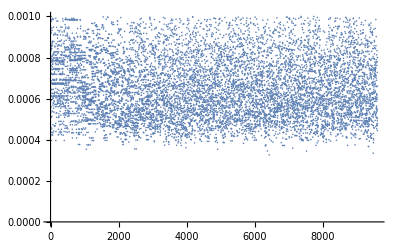

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}